```mathematica
(*grades, anonymized, post-first stage processing*)
grades={{4,4,0,4,3,4,4,2,0,0,25},{4,4,4,4,4,3,6,2,1,0,32},{4,2,4,1,1,2,4,0,0,0,18},{4,3,4,2,2,2,6,0,2,1,26},{4,2,4,4,4,3,6,2,2,2,33},{4,4,4,4,4,4,6,2,2,2,36},{4,4,1,4,4,4,6,2,2,1,32},{2,4,2,4,1,2,2,0,0,0,17},{4,0,2,2,0,0,0,0,1,0,9},{4,4,4,4,4,4,6,2,2,2,36},{4,4,4,4,4,3,6,2,1,0,32},{3,3,2,2,1,0,1,0,0,0,12},{3,4,4,2,3,2,5,2,1,0,26},{4,4,4,2,3,3,6,2,2,1,31},{3,4,4,4,2,2,6,2,1,1,29},{4,4,0,2,4,2,0,1,1,0,18},{4,4,2,3,4,4,3,2,1,1,28},{4,4,4,3,4,2,5,0,1,1,28},{4,4,3,4,3,4,6,2,1,2,33},{4,4,4,3,4,4,6,2,0,2,33},{4,4,4,3,4,4,4,2,2,1,32},{4,3,4,4,4,4,6,2,2,2,35},{4,4,4,3,4,3,6,2,2,2,34},{4,4,4,2,4,3,6,2,2,1,32},{4,4,2,1,0,0,0,2,1,0,14},{2,0,1,0,0,0,0,0,0,0,3},{4,4,4,4,4,4,6,2,2,1,35},{2,0,3,1,0,0,0,0,0,0,6},{4,4,2,3,3,0,5,2,0,0,23},{4,4,4,4,4,4,5,2,2,1,34},{4,4,4,4,4,3,6,2,2,2,35},{4,4,1,1,1,0,1,0,0,0,12}};
scores=Transpose[grades];
```

```mathematica
(*compute correlation matrix*)
corr=ConstantArray[0,{Length[scores],Length[scores]}];
For[i=1,i≤Length[scores],i++,
For[j=1,j≤Length[scores],j++,
corr[[i]][[j]]=N[Correlation[scores[[i]],scores[[j]]]];
]
]
```

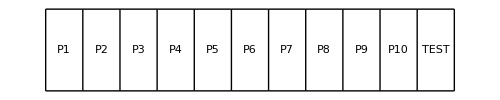
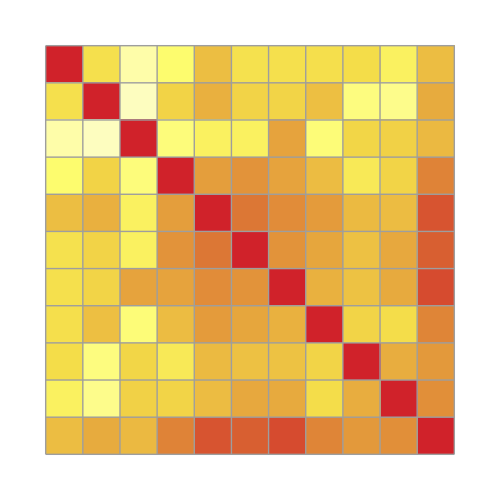
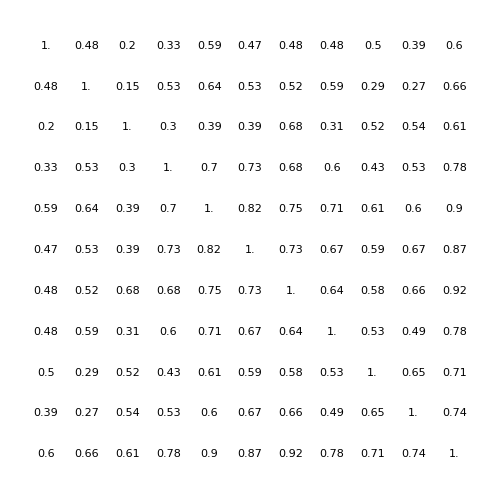
-Graphics-
-Graphics--Graphics--Graphics-

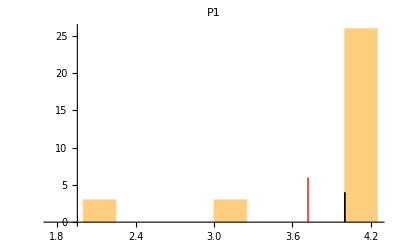
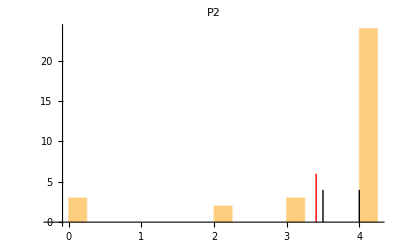
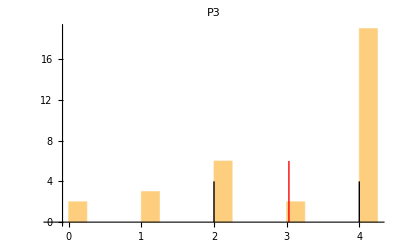
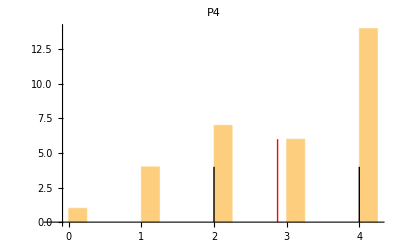
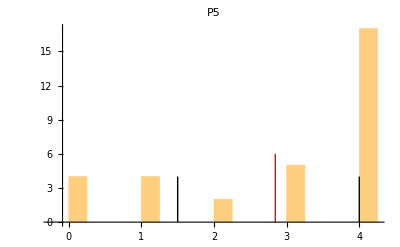
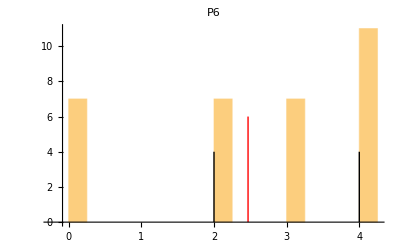
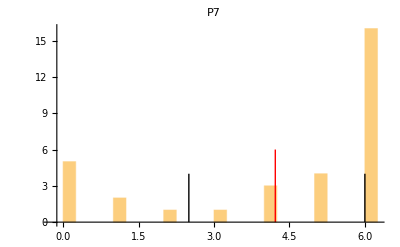
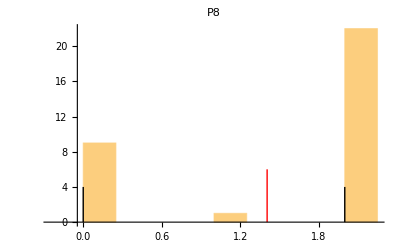

-Graphics-

```mathematica
(*labels for the correlation array*)
labels={P1,P2,P3,P4,P5,P6,P7,P8,P9,P10,TEST};
(*Fancy picture*)
Column[{GraphicsRow[labels,ImageSize->500,Frame->All],Row[{GraphicsColumn[labels,ImageSize->46,Frame->All],Overlay[{ArrayPlot[corr,ColorFunction->(ColorData["TemperatureMap"][(1+#)/2]&),Frame->None,Mesh->True,PlotRangePadding->0,ImageSize->500,ColorFunctionScaling->False],GraphicsGrid[Map[NumberForm[#,2]&,corr,{2}],ImageSize->500]}]}]},Alignment->Right,Spacings->0]
(*histograms,for,each,problem,&,test,as,a,whole*)
histograms={};
For[i=1,i≤Length[scores],i++,
histograms=Append[histograms,Histogram[scores[[i]],{.25},Epilog->{Directive[{Thick,Red}],Line[{{Mean[scores[[i]]],0},{Mean[scores[[i]]],6}}],{Directive[{Thick,Black}],Line[{{Quartiles[scores[[i]]][[1]],0},{Quartiles[scores[[i]]][[1]],4}}],Line[{{Quartiles[scores[[i]]][[3]],0},{Quartiles[scores[[i]]][[3]],4}}]}},PlotLabel->labels[[i]]]];
]
histograms
histograms[[Length[histograms]]]
```

```mathematica
(*range of scores: 20 to 37*)
(*this is where we'll draw the D to A range (traditionally: 60 to 100)*)
```